```mathematica
ViewProgress[net_,t_]:=(ImageResize[#1,75]&)/@NetChain[{NetExtract[net,1]},"Output"->NetDecoder[{"Image"}]][t]
```

```mathematica
wGANgenerator=
NetChain[
{LinearLayer[256],
ElementwiseLayer[Ramp],
LinearLayer[512],
ElementwiseLayer[Ramp],
ReshapeLayer[{32,4,4}],
DeconvolutionLayer[16,6,"Stride"->2],
ElementwiseLayer[Ramp],
DeconvolutionLayer[1,6,"Stride"->2],
ElementwiseLayer[LogisticSigmoid]},
"Input"->latentDim]
```

NetChain[<>]

```mathematica
wGANdiscriminator=
NetChain[
{
ConvolutionLayer[16,6,"Stride"->2],ElementwiseLayer[Ramp],
ConvolutionLayer[32,6,"Stride"->2],ElementwiseLayer[Ramp],
FlattenLayer[],
LinearLayer[256],ElementwiseLayer[Ramp],
LinearLayer[1]},
"Input"->imageDims
]
```

NetChain[<>]

```mathematica
wGAN=
NetGraph[
<|"generator"->wGANgenerator,
"discriminator"->NetChain[{ReshapeLayer[Prepend[imageDims,2]],NetMapOperator[wGANdiscriminator]}],"combine"->CatenateLayer[],"loss"->NetChain[{LinearLayer[1,"Weights"->{{-1,1}},"Biases"->{0}],PartLayer[1]},"Input"->{2,1}]|>,
{NetPort["Random"]->"generator"->"combine",NetPort["Input"]->"combine","combine"->"discriminator"->"loss"},"Input"->NetEncoder[{"Image",Rest@imageDims,"Grayscale"}],"Random"->latentDim]
```

NetGraph[<>]

```mathematica
trainingData=<|"Random"->RandomReal[{-1,1},{Length[trainingData],latentDim}],"Input"->Keys@trainingData|>;
```

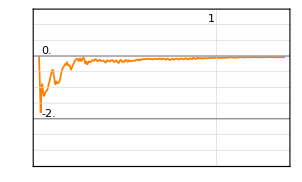
NetTrain Results
summary | ,,  batches:83012  rounds:2  time:5.6min  examples/s:245
data | ,,  training examples:60000  processed examples:83012  skipped examples:0
method | ,,  ADAMoptimizer  batch size1CPU
round | ,,  loss:-2.27×10^-1
 | rounds
loss | -Graphics- | 
 |

```mathematica
result=NetTrain[wGAN,trainingData,All,LossFunction->"Output",Method->{"ADAM","Beta1"->0.5,"LearningRate"->0.00005,"WeightClipping"->{"discriminator"->0.01}},"LearningRateMultipliers"->{"loss"->0,"generator"->-0.2},BatchSize->1,MaxTrainingRounds->1000,TrainingProgressReporting->{Function[Panel[Panel[
TextGrid[
{{Text[Style["",FontSize->12,TextAlignment->Center]]},
{TextCell["ROUND:",FontSize->12,"SuggestionsBarText"],
TextCell[ToString[#Round]<>" of "<>ToString[#TotalRounds],FontSize->12]},
{TextCell["TIME ELAPSED:",FontSize->12,"SuggestionsBarText"],TextCell[ToString[UnitConvert[Quantity[#TimeElapsed,"Milliseconds"],"Seconds"]],FontSize->12]},
{TextCell["TIME REMAINING:",FontSize->12,"SuggestionsBarText"],TextCell[ToString[UnitConvert[Quantity[#TimeRemaining,"Milliseconds"],"Seconds"]],FontSize->12]},
{TextCell["EXAPLES PROCESSED:",FontSize->12,"SuggestionsBarText"],TextCell[ToString[#ExamplesProcessed],FontSize->12]},
{TextCell["EXAMPLES PER SECOND:",FontSize->12,"SuggestionsBarText"],TextCell[ToString[#ExamplesPerSecond],FontSize->12]},
{TextCell["",FontSize->12,"SuggestionsBarText"],TextCell["",FontSize->12]},
{TextCell["TARGET DEVICE:",FontSize->12,"SuggestionsBarText"],
TextCell[ToString[#TargetDevice],FontSize->12]},
{TextCell["OPTIMIZATION METHOD:",FontSize->12,"SuggestionsBarText"],TextCell[ToString[#OptimizationMethod],FontSize->12]},
{TextCell["INITIAL LEARNING RATE:",FontSize->12,"SuggestionsBarText"],TextCell[ToString[#InitialLearningRate],FontSize->12]},
{TextCell["LEARNING RATE:",FontSize->12,"SuggestionsBarText"],TextCell[ToString[#LearningRate],FontSize->12]}
}],Grid[{ViewProgress[#Net,RandomReal[{-1,1},{Length[trainingData]*2,latentDim}]]}]]]],"Interval"->0.1},Method->{"ADAM","LearningRate"->0.0005}]
```

```mathematica
(
```

```mathematica
RandomReal[{-1,1},{Length[trainingData]*2,(latentDim)}]
```

{{0.0894558,-0.774609,0.924127,0.590388,-0.569075,-0.736736,-0.569477,0.34568},{-0.860918,0.388777,-0.35227,0.58488,0.176335,-0.345043,-0.75925,-0.601741},{0.469664,-0.0152973,0.0908665,-0.763102,-0.286428,-0.512436,0.0870367,-0.141713},{-0.714868,0.947322,-0.121682,0.0262022,0.931954,-0.575519,0.331257,-0.127344}}

```mathematica
Dimensions[%790]
```

{4,8}